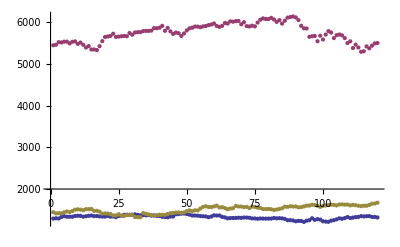

```mathematica
{hedge,dax,d2}=Transpose[Import["c:\\kurse.dat","Table"]];ListPlot[{hedge,dax,d2}]
```

```mathematica
hedge=Log[hedge];dax=Log[dax];d2=Log[d2];
```

```mathematica
hedge=Differences[hedge];
```

```mathematica
dax=Differences[dax];d2=Differences[d2];
```

```mathematica
w=Transpose[{hedge,dax,d2}];
```

```mathematica
w=Sort[w,#1[[1]]<#2[[1]]&];
```

```mathematica
hedge=Transpose[w][[1]];
dax=Transpose[w][[2]];
d2=Transpose[w][[3]];
```

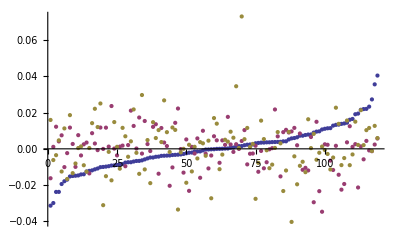

```mathematica
ListPlot[Transpose[w][[1;;3]],PlotRange->All]
```

```mathematica
min0=Min[Transpose[w][[1]]];wN=Length[hedge];nn=wN;
max0=Max[Transpose[w][[1]]];
min1=Min[Transpose[w][[2]]];
max1=Max[Transpose[w][[2]]];
```

```mathematica
U={};sdax=Sort[dax];AppendTo[U,{max0,max1,1}];

For[i=1,i≤nn,i++,
AppendTo[U,{hedge[[i]],max1,(i-1)/nn}];
AppendTo[U,{max0,sdax[[i]],(i-1)/nn}];
AppendTo[U,{hedge[[i]],min1,0}];
AppendTo[U,{min0,sdax[[i]],0}];
]
```

```mathematica
F={};For[i=1,i≤wN,i++,
AppendTo[F,{w[[i,1]],w[[i,2]],Length[Select[w,#[[1]]<=w[[i,1]]  && #[[2]]<=w[[i,2]]&]]/wN}];
]
```

```mathematica
W=Join[F,U];
```

```mathematica
ListPointPlot3D[W]
```

-Graphics3D-

```mathematica
hedgeI=Table[{hedge[[i]],(i-1)/(nn-1)},{i,nn}];
daxI=Table[{sdax[[i]],(i-1)/(nn-1)},{i,nn}];W=F;Co=Table[{Select[hedgeI,#[[1]]==W[[i,1]]&][[1,2]],Select[daxI,#[[1]]==W[[i,2]]&][[1,2]],W[[i,3]]},{i,Length[W]}];AppendTo[Co,{1,0,0}];AppendTo[Co,{0,1,0}];AppendTo[Co,{0,0,0}];AppendTo[Co,{1,1,1}];
```

```mathematica
ListPointPlot3D[Co]
```

-Graphics3D-

```mathematica
dg=Import["D:\\Dateien\\NetBeansProjects\\HedgeFit\\CopulaDSample.dat","Table"];g=Import["D:\\Dateien\\NetBeansProjects\\HedgeFit\\CopulaSample.dat","Table"];dbe=Import["D:\\Dateien\\NetBeansProjects\\HedgeFit\\CopulaB.dat","Table"];h=Import["D:\\Dateien\\NetBeansProjects\\HedgeFit\\delaunay.dat","Table"];
cc=Import["D:\\Dateien\\NetBeansProjects\\HedgeFit\Copula.dat","Table"];c=Transpose[{#[[1]],#[[2]],#[[3]]}&[Transpose[cc]]];cc=Transpose[Transpose[cc][[1;;3]]];hh=h;
Graphics3D[{{PointSize[Large],Red,Table[Point[c[[i]]],{i,Length[c]}]},{PointSize[Large],Point[{{107.4,25,22.51310344827582
}}]},{Opacity[1],Table[Polygon[c[[#+1]]&/@hh[[j]]],{j,Length[hh]}]}}]
```

-Graphics3D-

```mathematica
dd=Transpose[Transpose[cc][[1;;2]]];
```

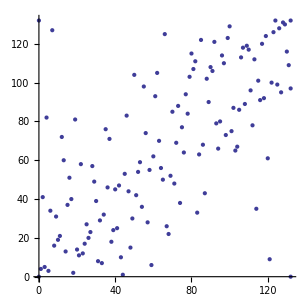

```mathematica
ListPlot[dd,AspectRatio->1]
```

```mathematica
dd={{92,121},{107,118},{58,55},{83,33},{18,2},{24,17},{47,44},{85,122},{40,45},{84,63},{100,129},{129,130},{103,65},{60,62},{55,98},{43,10},{45,53},{29,49},{39,24},{49,30},{99,123},{97,110},{114,35},{106,113},{78,84},{68,22},{115,101},{105,86},{38,18},{67,26},{126,128},{89,90},{35,76},{41,25},{59,6},{80,115},{48,15},{91,106},{31,8},{20,14},{5,3},{32,29},{76,64},{123,126},{8,16},{50,104},{26,20},{12,72},{81,107},{96,114},{3,5},{23,12},{7,127},{6,34},{4,82},{1,4},{117,120},{102,87},{93,79},{131,109},{101,75},{120,61},{71,48},{9,31},{98,73},{82,111},{119,124},{56,74},{90,108},{33,7},{73,88},{44,1},{25,27},{113,112},{75,77},{62,105},{74,38},{65,50},{130,116},{128,131},{69,52},{88,102},{53,59},{16,51},{108,89},{132,97},{63,70},{79,103},{70,85},{37,71},{64,56},{125,99},{42,47},{104,67},{86,68},{77,94},{72,69},{27,23},{22,58},{46,83},{57,28},{17,40},{11,21},{127,95},{52,54},{110,117},{112,78},{122,100},{51,42},{116,91},{121,9},{2,41},{15,37},{95,80},{36,46},{19,81},{28,57},{13,60},{87,43},{94,66},{21,11},{34,32},{10,19},{66,125},{14,13},{61,93},{111,96},{54,36},{30,39},{124,132},{118,92},{109,119}};
```

```mathematica
wN=Length[dd];n=Round[Sqrt[wN]*1.1];F={};For[i=0,i≤n,i++,
For[j=0,j≤n,j++,
If[i==0,AppendTo[F,{i/n,j/n,0}],If[j==0,AppendTo[F,{i/n,j/n,0}],If[i==n,AppendTo[F,{i/n,j/n,j/n}],If[j==n,AppendTo[F,{i/n,j/n,i/n}],
AppendTo[F,{i/n,j/n,Length[Select[dd,#[[1]]≤i wN/n&&#[[2]]≤j wN/n&]]/wN}]]]]]
]];iF=Table[F[[(n+1)(i-1)+j,3]],{i,1,n+1},{j,1,n+1}];
```

```mathematica
ListPointPlot3D[{cc/wN,F}]
```

-Graphics3D-

```mathematica
Show[ListPointPlot3D[cc/wN,PlotStyle->PointSize[Medium]],ListPlot3D[F]]
```

-Graphics3D-

```mathematica
,
```

```mathematica
iF=Table[{#[[1]],#[[2]],#[[3]]}&[F[[(n+1)(i-1)+j]]],{i,1,n+1},{j,1,n+1}];
```

```mathematica
ListPointPlot3D[iF[[3]]]
```

-Graphics3D-

```mathematica
dF=Table[{iF[[i,j,1]],iF[[i,j,2]],iF[[i+1,j+1,3]]+iF[[i-1,j-1,3]]-iF[[i+1,j-1,3]]-iF[[i-1,j+1,3]]},{i,2,n-1},{j,2,n-1}];
```

```mathematica
ListPointPlot3D[dF]
```

-Graphics3D-

```mathematica
G=Table[g[[Sqrt[Length[g]]*(i-1)+j,3]],{i,Sqrt[Length[g]]},{j,Sqrt[Length[g]]}];
```

```mathematica
B=Table[be[[Sqrt[Length[be]]*(i-1)+j,3]],{i,Sqrt[Length[be]]},{j,Sqrt[Length[be]]}];
```

```mathematica
{ListPlot3D[{dg }],ListPlot3D[{dbe }]}
```

{-Graphics3D-,-Graphics3D-}

```mathematica
ifun = ListInterpolation[G, {{0,1},{0,1}},InterpolationOrder->5]
```

InterpolatingFunction[{{0.,1.},{0.,1.}},<>]

```mathematica
Plot3D[D[ifun[xx,y],xx]/.xx->x,{x,0,1},{y,0,1},PlotRange->{0,1}]
```

-Graphics3D-

```mathematica
f[x_,y_]:=x y
```

```mathematica
y
```

y

```mathematica
Plot3D[D[f[xx,y],xx]/.xx->x,{x,0,1},{y,0,1}]
```

-Graphics3D-

```mathematica
ListPointPlot3D[dbe]
```

-Graphics3D-

```mathematica
ListPointPlot3D[Table[{be[[i,1]],be[[i,2]],be[[i,3]]-ifun[be[[i,1]],be[[i,2]]]},{i,Length[be]}]]
```

-Graphics3D-

```mathematica
Show[%,ListPointPlot3D[{{11.9,23.8,0}}]]
```

-Graphics3D-

```mathematica
Length[h]
```

240

```mathematica
h[[123]]
```

{26,34,78}

```mathematica
Length[c]
```

122

```mathematica
h
```

{{0,7,19},{0,7,67},{0,12,57},{0,12,82},{0,19,57},{0,24,66},{0,24,67},{0,32,66},{0,32,82},{1,41,62},{1,41,100},{1,49,54},{1,49,62},{1,54,76},{1,76,117},{1,100,117},{2,44,94},{2,80,92},{2,80,101},{2,92,94},{2,94,121},{2,101,107},{2,101,121},{3,12,57},{3,12,58},{3,57,104},{3,58,104},{4,14,30},{4,14,37},{4,30,35},{4,31,35},{4,31,71},{4,37,105},{4,53,71},{4,53,105},{5,15,65},{5,15,115},{5,43,60},{5,43,115},{5,60,65},{6,9,51},{6,9,117},{6,32,47},{6,32,79},{6,47,117},{6,51,79},{7,19,104},{7,23,25},{7,23,104},{7,25,34},{7,34,67},{8,13,46},{8,13,111},{8,28,89},{8,28,115},{8,46,89},{8,111,115},{9,51,76},{9,76,117},{10,22,81},{10,22,91},{10,81,88},{10,88,91},{11,13,46},{11,13,109},{11,42,102},{11,42,106},{11,46,89},{11,89,106},{11,102,109},{12,44,58},{12,44,103},{12,69,82},{12,69,103},{13,70,90},{13,70,111},{13,90,109},{14,30,95},{14,37,95},{15,28,45},{15,28,115},{15,45,65},{16,17,74},{16,17,99},{16,48,74},{16,48,99},{17,18,100},{17,18,114},{17,27,74},{17,27,100},{17,97,99},{17,97,114},{17,97,122},{17,114,122},{18,47,114},{18,47,117},{18,100,117},{19,57,104},{20,30,95},{20,30,118},{20,50,56},{20,50,95},{20,56,72},{20,72,118},{21,29,36},{21,29,64},{21,36,47},{21,47,82},{21,64,82},{22,40,83},{22,40,98},{22,40,119},{22,81,83},{22,91,98},{22,98,119},{23,25,92},{23,92,94},{23,94,104},{24,38,78},{24,38,86},{24,66,86},{24,67,78},{25,34,80},{25,80,92},{26,28,34},{26,28,45},{26,34,78},{26,45,65},{26,65,78},{27,41,48},{27,41,100},{27,48,74},{28,34,80},{28,80,89},{29,36,75},{29,64,69},{29,69,75},{30,35,118},{31,35,118},{31,52,55},{31,52,71},{31,55,87},{31,87,118},{32,47,82},{32,66,79},{33,38,55},{33,38,78},{33,52,55},{33,52,77},{33,65,77},{33,65,78},{34,67,78},{36,47,114},{36,75,114},{37,63,88},{37,63,95},{37,88,105},{38,51,76},{38,51,86},{38,54,55},{38,54,76},{39,49,56},{39,49,116},{39,56,61},{39,61,108},{39,108,116},{40,68,83},{40,68,90},{40,90,98},{40,90,119},{41,48,62},{42,96,102},{42,96,112},{42,101,106},{42,101,107},{42,107,112},{43,59,60},{43,59,68},{43,68,70},{43,70,111},{43,111,115},{44,58,94},{44,94,121},{44,103,122},{48,62,84},{48,84,97},{48,97,99},{49,54,113},{49,56,72},{49,62,84},{49,72,113},{49,84,116},{50,56,61},{50,61,95},{51,79,86},{52,71,77},{53,59,77},{53,59,81},{53,71,77},{53,81,105},{54,55,113},{55,87,113},{58,94,104},{59,60,73},{59,68,83},{59,73,77},{59,81,83},{60,65,73},{61,85,95},{61,85,108},{61,85,120},{61,95,120},{63,88,91},{63,91,95},{64,69,82},{65,73,77},{66,79,86},{68,70,90},{69,75,103},{72,87,113},{72,87,118},{75,103,110},{75,110,114},{80,89,106},{80,101,106},{81,88,105},{84,97,116},{85,95,98},{85,95,119},{85,97,116},{85,97,120},{85,108,116},{85,116,120},{90,93,109},{90,93,119},{91,95,98},{93,96,102},{93,96,107},{93,96,121},{93,102,109},{93,119,121},{95,98,119},{95,98,120},{95,119,120},{96,107,112},{96,107,121},{97,116,120},{101,107,121},{103,110,122},{110,114,122}}

```mathematica
ce=c[[3;;7]];
```

```mathematica
ce={{0.23564142713114022,0.19380998628864599,0.594495511815069},{0.6525572153791819,0.24694329925782044,0.7672917678839029},{0.9163123444125463,0.026621532304647255,0.3715576391209683},{0.2668950744537262,0.7975001767040044,0.7934023887167383},{0.7641225411392012,0.2966207983489944,0.1456840182999719}}
```

{{0.235641,0.19381,0.594496},{0.652557,0.246943,0.767292},{0.916312,0.0266215,0.371558},{0.266895,0.7975,0.793402},{0.764123,0.296621,0.145684}}

```mathematica
{{0.23564142713114022,0.19380998628864599,0.594495511815069},{0.6525572153791819,0.24694329925782044,0.7672917678839029},{0.3163123444125463,0.026621532304647255,0.3715576391209683},{0.2668950744537262,0.7975001767040044,0.7934023887167383},{0.7641225411392012,0.8966207983489944,0.1456840182999719}}
```

```mathematica
ListPointPlot3D[{ce,  {a}},PlotStyle->PointSize[Large]]
```

-Graphics3D-

```mathematica
a={1,2,3};
```

```mathematica
Det[
```

```mathematica
Export["c:\\empCopula.dat",RandomReal[1,{7,4}]]
```

c:\empCopula.dat

-Graphics3D-

```mathematica
ListPointPlot3D[cc,PlotStyle->PointSize[Large]]
```

-Graphics3D-

```mathematica
Show[ListPointPlot3D[{#[[1]],#[[2]],#[[3]]+0.01}&/@c,PlotStyle->Red],ListPointPlot3D[Co]]
```

-Graphics3D-

```mathematica
Show[ListPlot3D[c,Mesh->All],ListPointPlot3D[c,PlotStyle->Red],AspectRatio->1]
```

-Graphics3D-

```mathematica
y=.
```

```mathematica
Plot3D[Interpolation[c][x,y],{x,0,1},{y,0,1}]
```

Interpolation::indim: The coordinates do not lie on a structured tensor product grid.

General::stop: Further output of Interpolation :: "indim" will be suppressed during this calculation.

-Graphics3D-

```mathematica
Graphics3D[{{PointSize[Large],Red,Table[Point[c[[i]]],{i,Length[c]}]},{Table[Polygon[c[[#+1]]&/@h[[j]]],{j,Length[h]}]}}]
```

-Graphics3D-

```mathematica
ListPointPlot3D[{g}]
```

-Graphics3D-

```mathematica
Show[ListPointPlot3D[c,PlotStyle->Red],ListPlot3D[g,InterpolationOrder->1,Mesh->{20,20}],AspectRatio->1]
```

-Graphics3D-

```mathematica
f[i_]:={C[i][0],C[i][1],C[i][2],C[i][0]^2+C[i][1]^2+C[i][2]^2};Det[{f[h],f[i],f[j],f[k]}]
```

C[h][2] C[i][1] (C[j][0])^2 C[k][0]-C[h][1] C[i][2] (C[j][0])^2 C[k][0]-C[h][2] (C[i][0])^2 C[j][1] C[k][0]-C[h][2] (C[i][1])^2 C[j][1] C[k][0]+(C[h][0])^2 C[i][2] C[j][1] C[k][0]+(C[h][1])^2 C[i][2] C[j][1] C[k][0]+(C[h][2])^2 C[i][2] C[j][1] C[k][0]-C[h][2] (C[i][2])^2 C[j][1] C[k][0]+C[h][2] C[i][1] (C[j][1])^2 C[k][0]-C[h][1] C[i][2] (C[j][1])^2 C[k][0]+C[h][1] (C[i][0])^2 C[j][2] C[k][0]-(C[h][0])^2 C[i][1] C[j][2] C[k][0]-(C[h][1])^2 C[i][1] C[j][2] C[k][0]-(C[h][2])^2 C[i][1] C[j][2] C[k][0]+C[h][1] (C[i][1])^2 C[j][2] C[k][0]+C[h][1] (C[i][2])^2 C[j][2] C[k][0]+C[h][2] C[i][1] (C[j][2])^2 C[k][0]-C[h][1] C[i][2] (C[j][2])^2 C[k][0]-C[h][2] C[i][1] C[j][0] (C[k][0])^2+C[h][1] C[i][2] C[j][0] (C[k][0])^2+C[h][2] C[i][0] C[j][1] (C[k][0])^2-C[h][0] C[i][2] C[j][1] (C[k][0])^2-C[h][1] C[i][0] C[j][2] (C[k][0])^2+C[h][0] C[i][1] C[j][2] (C[k][0])^2+C[h][2] (C[i][0])^2 C[j][0] C[k][1]+C[h][2] (C[i][1])^2 C[j][0] C[k][1]-(C[h][0])^2 C[i][2] C[j][0] C[k][1]-(C[h][1])^2 C[i][2] C[j][0] C[k][1]-(C[h][2])^2 C[i][2] C[j][0] C[k][1]+C[h][2] (C[i][2])^2 C[j][0] C[k][1]-C[h][2] C[i][0] (C[j][0])^2 C[k][1]+C[h][0] C[i][2] (C[j][0])^2 C[k][1]-C[h][2] C[i][0] (C[j][1])^2 C[k][1]+C[h][0] C[i][2] (C[j][1])^2 C[k][1]+(C[h][0])^2 C[i][0] C[j][2] C[k][1]+(C[h][1])^2 C[i][0] C[j][2] C[k][1]+(C[h][2])^2 C[i][0] C[j][2] C[k][1]-C[h][0] (C[i][0])^2 C[j][2] C[k][1]-C[h][0] (C[i][1])^2 C[j][2] C[k][1]-C[h][0] (C[i][2])^2 C[j][2] C[k][1]-C[h][2] C[i][0] (C[j][2])^2 C[k][1]+C[h][0] C[i][2] (C[j][2])^2 C[k][1]-C[h][2] C[i][1] C[j][0] (C[k][1])^2+C[h][1] C[i][2] C[j][0] (C[k][1])^2+C[h][2] C[i][0] C[j][1] (C[k][1])^2-C[h][0] C[i][2] C[j][1] (C[k][1])^2-C[h][1] C[i][0] C[j][2] (C[k][1])^2+C[h][0] C[i][1] C[j][2] (C[k][1])^2-C[h][1] (C[i][0])^2 C[j][0] C[k][2]+(C[h][0])^2 C[i][1] C[j][0] C[k][2]+(C[h][1])^2 C[i][1] C[j][0] C[k][2]+(C[h][2])^2 C[i][1] C[j][0] C[k][2]-C[h][1] (C[i][1])^2 C[j][0] C[k][2]-C[h][1] (C[i][2])^2 C[j][0] C[k][2]+C[h][1] C[i][0] (C[j][0])^2 C[k][2]-C[h][0] C[i][1] (C[j][0])^2 C[k][2]-(C[h][0])^2 C[i][0] C[j][1] C[k][2]-(C[h][1])^2 C[i][0] C[j][1] C[k][2]-(C[h][2])^2 C[i][0] C[j][1] C[k][2]+C[h][0] (C[i][0])^2 C[j][1] C[k][2]+C[h][0] (C[i][1])^2 C[j][1] C[k][2]+C[h][0] (C[i][2])^2 C[j][1] C[k][2]+C[h][1] C[i][0] (C[j][1])^2 C[k][2]-C[h][0] C[i][1] (C[j][1])^2 C[k][2]+C[h][1] C[i][0] (C[j][2])^2 C[k][2]-C[h][0] C[i][1] (C[j][2])^2 C[k][2]-C[h][2] C[i][1] C[j][0] (C[k][2])^2+C[h][1] C[i][2] C[j][0] (C[k][2])^2+C[h][2] C[i][0] C[j][1] (C[k][2])^2-C[h][0] C[i][2] C[j][1] (C[k][2])^2-C[h][1] C[i][0] C[j][2] (C[k][2])^2+C[h][0] C[i][1] C[j][2] (C[k][2])^2

```mathematica
CForm[Expand[%]]
```

C(h)(2)*C(i)(1)*Power(C(j)(0),2)*C(k)(0) - C(h)(1)*C(i)(2)*Power(C(j)(0),2)*C(k)(0) - C(h)(2)*Power(C(i)(0),2)*C(j)(1)*C(k)(0) - 
   C(h)(2)*Power(C(i)(1),2)*C(j)(1)*C(k)(0) + Power(C(h)(0),2)*C(i)(2)*C(j)(1)*C(k)(0) + 
   Power(C(h)(1),2)*C(i)(2)*C(j)(1)*C(k)(0) + Power(C(h)(2),2)*C(i)(2)*C(j)(1)*C(k)(0) - 
   C(h)(2)*Power(C(i)(2),2)*C(j)(1)*C(k)(0) + C(h)(2)*C(i)(1)*Power(C(j)(1),2)*C(k)(0) - 
   C(h)(1)*C(i)(2)*Power(C(j)(1),2)*C(k)(0) + C(h)(1)*Power(C(i)(0),2)*C(j)(2)*C(k)(0) - 
   Power(C(h)(0),2)*C(i)(1)*C(j)(2)*C(k)(0) - Power(C(h)(1),2)*C(i)(1)*C(j)(2)*C(k)(0) - 
   Power(C(h)(2),2)*C(i)(1)*C(j)(2)*C(k)(0) + C(h)(1)*Power(C(i)(1),2)*C(j)(2)*C(k)(0) + 
   C(h)(1)*Power(C(i)(2),2)*C(j)(2)*C(k)(0) + C(h)(2)*C(i)(1)*Power(C(j)(2),2)*C(k)(0) - 
   C(h)(1)*C(i)(2)*Power(C(j)(2),2)*C(k)(0) - C(h)(2)*C(i)(1)*C(j)(0)*Power(C(k)(0),2) + 
   C(h)(1)*C(i)(2)*C(j)(0)*Power(C(k)(0),2) + C(h)(2)*C(i)(0)*C(j)(1)*Power(C(k)(0),2) - 
   C(h)(0)*C(i)(2)*C(j)(1)*Power(C(k)(0),2) - C(h)(1)*C(i)(0)*C(j)(2)*Power(C(k)(0),2) + 
   C(h)(0)*C(i)(1)*C(j)(2)*Power(C(k)(0),2) + C(h)(2)*Power(C(i)(0),2)*C(j)(0)*C(k)(1) + 
   C(h)(2)*Power(C(i)(1),2)*C(j)(0)*C(k)(1) - Power(C(h)(0),2)*C(i)(2)*C(j)(0)*C(k)(1) - 
   Power(C(h)(1),2)*C(i)(2)*C(j)(0)*C(k)(1) - Power(C(h)(2),2)*C(i)(2)*C(j)(0)*C(k)(1) + 
   C(h)(2)*Power(C(i)(2),2)*C(j)(0)*C(k)(1) - C(h)(2)*C(i)(0)*Power(C(j)(0),2)*C(k)(1) + 
   C(h)(0)*C(i)(2)*Power(C(j)(0),2)*C(k)(1) - C(h)(2)*C(i)(0)*Power(C(j)(1),2)*C(k)(1) + 
   C(h)(0)*C(i)(2)*Power(C(j)(1),2)*C(k)(1) + Power(C(h)(0),2)*C(i)(0)*C(j)(2)*C(k)(1) + 
   Power(C(h)(1),2)*C(i)(0)*C(j)(2)*C(k)(1) + Power(C(h)(2),2)*C(i)(0)*C(j)(2)*C(k)(1) - 
   C(h)(0)*Power(C(i)(0),2)*C(j)(2)*C(k)(1) - C(h)(0)*Power(C(i)(1),2)*C(j)(2)*C(k)(1) - 
   C(h)(0)*Power(C(i)(2),2)*C(j)(2)*C(k)(1) - C(h)(2)*C(i)(0)*Power(C(j)(2),2)*C(k)(1) + 
   C(h)(0)*C(i)(2)*Power(C(j)(2),2)*C(k)(1) - C(h)(2)*C(i)(1)*C(j)(0)*Power(C(k)(1),2) + 
   C(h)(1)*C(i)(2)*C(j)(0)*Power(C(k)(1),2) + C(h)(2)*C(i)(0)*C(j)(1)*Power(C(k)(1),2) - 
   C(h)(0)*C(i)(2)*C(j)(1)*Power(C(k)(1),2) - C(h)(1)*C(i)(0)*C(j)(2)*Power(C(k)(1),2) + 
   C(h)(0)*C(i)(1)*C(j)(2)*Power(C(k)(1),2) - C(h)(1)*Power(C(i)(0),2)*C(j)(0)*C(k)(2) + 
   Power(C(h)(0),2)*C(i)(1)*C(j)(0)*C(k)(2) + Power(C(h)(1),2)*C(i)(1)*C(j)(0)*C(k)(2) + 
   Power(C(h)(2),2)*C(i)(1)*C(j)(0)*C(k)(2) - C(h)(1)*Power(C(i)(1),2)*C(j)(0)*C(k)(2) - 
   C(h)(1)*Power(C(i)(2),2)*C(j)(0)*C(k)(2) + C(h)(1)*C(i)(0)*Power(C(j)(0),2)*C(k)(2) - 
   C(h)(0)*C(i)(1)*Power(C(j)(0),2)*C(k)(2) - Power(C(h)(0),2)*C(i)(0)*C(j)(1)*C(k)(2) - 
   Power(C(h)(1),2)*C(i)(0)*C(j)(1)*C(k)(2) - Power(C(h)(2),2)*C(i)(0)*C(j)(1)*C(k)(2) + 
   C(h)(0)*Power(C(i)(0),2)*C(j)(1)*C(k)(2) + C(h)(0)*Power(C(i)(1),2)*C(j)(1)*C(k)(2) + 
   C(h)(0)*Power(C(i)(2),2)*C(j)(1)*C(k)(2) + C(h)(1)*C(i)(0)*Power(C(j)(1),2)*C(k)(2) - 
   C(h)(0)*C(i)(1)*Power(C(j)(1),2)*C(k)(2) + C(h)(1)*C(i)(0)*Power(C(j)(2),2)*C(k)(2) - 
   C(h)(0)*C(i)(1)*Power(C(j)(2),2)*C(k)(2) - C(h)(2)*C(i)(1)*C(j)(0)*Power(C(k)(2),2) + 
   C(h)(1)*C(i)(2)*C(j)(0)*Power(C(k)(2),2) + C(h)(2)*C(i)(0)*C(j)(1)*Power(C(k)(2),2) - 
   C(h)(0)*C(i)(2)*C(j)(1)*Power(C(k)(2),2) - C(h)(1)*C(i)(0)*C(j)(2)*Power(C(k)(2),2) + C(h)(0)*C(i)(1)*C(j)(2)*Power(C(k)(2),2)

```mathematica
f[k]
```

{C[k][0],C[k][1],C[k][2],C[i][0]*C[i][0]+C[i][1]*C[i][1]+C[i][2]*C[i][2],1}

```mathematica
Expand[Det[{f[h],f[i],f[j],f[k]}]]
```

-C[h][2] C[i][1] C[j][0]+C[h][1] C[i][2] C[j][0]+C[h][2] C[i][0] C[j][1]-C[h][0] C[i][2] C[j][1]-C[h][1] C[i][0] C[j][2]+C[h][0] C[i][1] C[j][2]+C[h][2] C[i][1] C[k][0]-C[h][1] C[i][2] C[k][0]-C[h][2] C[j][1] C[k][0]+C[i][2] C[j][1] C[k][0]+C[h][1] C[j][2] C[k][0]-C[i][1] C[j][2] C[k][0]-C[h][2] C[i][0] C[k][1]+C[h][0] C[i][2] C[k][1]+C[h][2] C[j][0] C[k][1]-C[i][2] C[j][0] C[k][1]-C[h][0] C[j][2] C[k][1]+C[i][0] C[j][2] C[k][1]+C[h][1] C[i][0] C[k][2]-C[h][0] C[i][1] C[k][2]-C[h][1] C[j][0] C[k][2]+C[i][1] C[j][0] C[k][2]+C[h][0] C[j][1] C[k][2]-C[i][0] C[j][1] C[k][2]

```mathematica
f[i_]:={C[i][0],C[i][1],C[i][2]};CForm[Expand[Det[{f[h],f[i],f[j]}]]]
```

-(C(h)(2)*C(i)(1)*C(j)(0)) + C(h)(1)*C(i)(2)*C(j)(0) + C(h)(2)*C(i)(0)*C(j)(1) - C(h)(0)*C(i)(2)*C(j)(1) - 
   C(h)(1)*C(i)(0)*C(j)(2) + C(h)(0)*C(i)(1)*C(j)(2)

```mathematica
a=Expand[Det[{f[h],f[i],f[j]}]]
```

-C[h][2] C[i][1] C[j][0]+C[h][1] C[i][2] C[j][0]+C[h][2] C[i][0] C[j][1]-C[h][0] C[i][2] C[j][1]-C[h][1] C[i][0] C[j][2]+C[h][0] C[i][1] C[j][2]+C[h][2] C[i][1] C[k][0]-C[h][1] C[i][2] C[k][0]-C[h][2] C[j][1] C[k][0]+C[i][2] C[j][1] C[k][0]+C[h][1] C[j][2] C[k][0]-C[i][1] C[j][2] C[k][0]-C[h][2] C[i][0] C[k][1]+C[h][0] C[i][2] C[k][1]+C[h][2] C[j][0] C[k][1]-C[i][2] C[j][0] C[k][1]-C[h][0] C[j][2] C[k][1]+C[i][0] C[j][2] C[k][1]+C[h][1] C[i][0] C[k][2]-C[h][0] C[i][1] C[k][2]-C[h][1] C[j][0] C[k][2]+C[i][1] C[j][0] C[k][2]+C[h][0] C[j][1] C[k][2]-C[i][0] C[j][1] C[k][2]

```mathematica
CForm[a]
```

-(C(h)(2)*C(i)(1)*C(j)(0)) + C(h)(1)*C(i)(2)*C(j)(0) + C(h)(2)*C(i)(0)*C(j)(1) - C(h)(0)*C(i)(2)*C(j)(1) - 
   C(h)(1)*C(i)(0)*C(j)(2) + C(h)(0)*C(i)(1)*C(j)(2) + C(h)(2)*C(i)(1)*C(k)(0) - C(h)(1)*C(i)(2)*C(k)(0) - 
   C(h)(2)*C(j)(1)*C(k)(0) + C(i)(2)*C(j)(1)*C(k)(0) + C(h)(1)*C(j)(2)*C(k)(0) - C(i)(1)*C(j)(2)*C(k)(0) - 
   C(h)(2)*C(i)(0)*C(k)(1) + C(h)(0)*C(i)(2)*C(k)(1) + C(h)(2)*C(j)(0)*C(k)(1) - C(i)(2)*C(j)(0)*C(k)(1) - 
   C(h)(0)*C(j)(2)*C(k)(1) + C(i)(0)*C(j)(2)*C(k)(1) + C(h)(1)*C(i)(0)*C(k)(2) - C(h)(0)*C(i)(1)*C(k)(2) - 
   C(h)(1)*C(j)(0)*C(k)(2) + C(i)(1)*C(j)(0)*C(k)(2) + C(h)(0)*C(j)(1)*C(k)(2) - C(i)(0)*C(j)(1)*C(k)(2)

```mathematica
b=Expand[Det[{f[h],f[i],f[j],f[k]}]]
```

-C[h][2] C[i][1] C[j][0]+C[h][1] C[i][2] C[j][0]+C[h][2] C[i][0] C[j][1]-C[h][0] C[i][2] C[j][1]-C[h][1] C[i][0] C[j][2]+C[h][0] C[i][1] C[j][2]+C[h][2] C[i][1] C[k][0]-C[h][1] C[i][2] C[k][0]-C[h][2] C[j][1] C[k][0]+C[i][2] C[j][1] C[k][0]+C[h][1] C[j][2] C[k][0]-C[i][1] C[j][2] C[k][0]-C[h][2] C[i][0] C[k][1]+C[h][0] C[i][2] C[k][1]+C[h][2] C[j][0] C[k][1]-C[i][2] C[j][0] C[k][1]-C[h][0] C[j][2] C[k][1]+C[i][0] C[j][2] C[k][1]+C[h][1] C[i][0] C[k][2]-C[h][0] C[i][1] C[k][2]-C[h][1] C[j][0] C[k][2]+C[i][1] C[j][0] C[k][2]+C[h][0] C[j][1] C[k][2]-C[i][0] C[j][1] C[k][2]

```mathematica
a-b
```

0

```mathematica
Needs["VectorAnalysis`"]
```

```mathematica
v[k_]:={C[k][0],C[k][1],C[k][2]};
```

```mathematica
n=CrossProduct[v[k]-v[i],v[j]-v[i]];Solve[({A[0],A[1],z}-v[i]).n==0,z][[1,1,2]]
```

(A[1] C[i][2] C[j][0]-A[0] C[i][2] C[j][1]-A[1] C[i][0] C[j][2]+A[0] C[i][1] C[j][2]-A[1] C[i][2] C[k][0]+C[i][2] C[j][1] C[k][0]+A[1] C[j][2] C[k][0]-C[i][1] C[j][2] C[k][0]+A[0] C[i][2] C[k][1]-C[i][2] C[j][0] C[k][1]-A[0] C[j][2] C[k][1]+C[i][0] C[j][2] C[k][1]+A[1] C[i][0] C[k][2]-A[0] C[i][1] C[k][2]-A[1] C[j][0] C[k][2]+C[i][1] C[j][0] C[k][2]+A[0] C[j][1] C[k][2]-C[i][0] C[j][1] C[k][2])/(C[i][1] C[j][0]-C[i][0] C[j][1]-C[i][1] C[k][0]+C[j][1] C[k][0]+C[i][0] C[k][1]-C[j][0] C[k][1])

```mathematica
D[%,A[0]]
```

(-C[i][2] C[j][1]+C[i][1] C[j][2]+C[i][2] C[k][1]-C[j][2] C[k][1]-C[i][1] C[k][2]+C[j][1] C[k][2])/(C[i][1] C[j][0]-C[i][0] C[j][1]-C[i][1] C[k][0]+C[j][1] C[k][0]+C[i][0] C[k][1]-C[j][0] C[k][1])

```mathematica
CForm[(A[1] C[i][2] C[j][0]-A[0] C[i][2] C[j][1]-A[1] C[i][0] C[j][2]+A[0] C[i][1] C[j][2]-A[1] C[i][2] C[k][0]+C[i][2] C[j][1] C[k][0]+A[1] C[j][2] C[k][0]-C[i][1] C[j][2] C[k][0]+A[0] C[i][2] C[k][1]-C[i][2] C[j][0] C[k][1]-A[0] C[j][2] C[k][1]+C[i][0] C[j][2] C[k][1]+A[1] C[i][0] C[k][2]-A[0] C[i][1] C[k][2]-A[1] C[j][0] C[k][2]+C[i][1] C[j][0] C[k][2]+A[0] C[j][1] C[k][2]-C[i][0] C[j][1] C[k][2])/(C[i][1] C[j][0]-C[i][0] C[j][1]-C[i][1] C[k][0]+C[j][1] C[k][0]+C[i][0] C[k][1]-C[j][0] C[k][1])]
```

(A(1)*C(i)(2)*C(j)(0) - A(0)*C(i)(2)*C(j)(1) - A(1)*C(i)(0)*C(j)(2) + A(0)*C(i)(1)*C(j)(2) - A(1)*C(i)(2)*C(k)(0) + C(i)(2)*C(j)(1)*C(k)(0) + A(1)*C(j)(2)*C(k)(0) - 
     C(i)(1)*C(j)(2)*C(k)(0) + A(0)*C(i)(2)*C(k)(1) - C(i)(2)*C(j)(0)*C(k)(1) - A(0)*C(j)(2)*C(k)(1) + C(i)(0)*C(j)(2)*C(k)(1) + A(1)*C(i)(0)*C(k)(2) - 
     A(0)*C(i)(1)*C(k)(2) - A(1)*C(j)(0)*C(k)(2) + C(i)(1)*C(j)(0)*C(k)(2) + A(0)*C(j)(1)*C(k)(2) - C(i)(0)*C(j)(1)*C(k)(2))/
   (C(i)(1)*C(j)(0) - C(i)(0)*C(j)(1) - C(i)(1)*C(k)(0) + C(j)(1)*C(k)(0) + C(i)(0)*C(k)(1) - C(j)(0)*C(k)(1))

```mathematica
Det[{{C[i][1],C[i][2],"C[i][1]*C[i][1]"+"C[i][2]*C[i][2]",1},{C[j][1],C[j][2],"C[j][1]*C[j][1]"+"C[j][2]*C[j][2]",1},{C[k][1],C[k][2],"C[k][1]*C[k][1]"+"C[k][2]*C[k][2]",1},{C[p][1],C[p][2],"C[p][1]*C[p][1]"+"C[p][2]*C[p][2]",1}}]
```

-C[k][1]*C[k][1] C[i][2] C[j][1]-C[k][2]*C[k][2] C[i][2] C[j][1]+C[p][1]*C[p][1] C[i][2] C[j][1]+C[p][2]*C[p][2] C[i][2] C[j][1]+C[k][1]*C[k][1] C[i][1] C[j][2]+C[k][2]*C[k][2] C[i][1] C[j][2]-C[p][1]*C[p][1] C[i][1] C[j][2]-C[p][2]*C[p][2] C[i][1] C[j][2]+C[j][1]*C[j][1] C[i][2] C[k][1]+C[j][2]*C[j][2] C[i][2] C[k][1]-C[p][1]*C[p][1] C[i][2] C[k][1]-C[p][2]*C[p][2] C[i][2] C[k][1]-C[i][1]*C[i][1] C[j][2] C[k][1]-C[i][2]*C[i][2] C[j][2] C[k][1]+C[p][1]*C[p][1] C[j][2] C[k][1]+C[p][2]*C[p][2] C[j][2] C[k][1]-C[j][1]*C[j][1] C[i][1] C[k][2]-C[j][2]*C[j][2] C[i][1] C[k][2]+C[p][1]*C[p][1] C[i][1] C[k][2]+C[p][2]*C[p][2] C[i][1] C[k][2]+C[i][1]*C[i][1] C[j][1] C[k][2]+C[i][2]*C[i][2] C[j][1] C[k][2]-C[p][1]*C[p][1] C[j][1] C[k][2]-C[p][2]*C[p][2] C[j][1] C[k][2]-C[j][1]*C[j][1] C[i][2] C[p][1]-C[j][2]*C[j][2] C[i][2] C[p][1]+C[k][1]*C[k][1] C[i][2] C[p][1]+C[k][2]*C[k][2] C[i][2] C[p][1]+C[i][1]*C[i][1] C[j][2] C[p][1]+C[i][2]*C[i][2] C[j][2] C[p][1]-C[k][1]*C[k][1] C[j][2] C[p][1]-C[k][2]*C[k][2] C[j][2] C[p][1]-C[i][1]*C[i][1] C[k][2] C[p][1]-C[i][2]*C[i][2] C[k][2] C[p][1]+C[j][1]*C[j][1] C[k][2] C[p][1]+C[j][2]*C[j][2] C[k][2] C[p][1]+C[j][1]*C[j][1] C[i][1] C[p][2]+C[j][2]*C[j][2] C[i][1] C[p][2]-C[k][1]*C[k][1] C[i][1] C[p][2]-C[k][2]*C[k][2] C[i][1] C[p][2]-C[i][1]*C[i][1] C[j][1] C[p][2]-C[i][2]*C[i][2] C[j][1] C[p][2]+C[k][1]*C[k][1] C[j][1] C[p][2]+C[k][2]*C[k][2] C[j][1] C[p][2]+C[i][1]*C[i][1] C[k][1] C[p][2]+C[i][2]*C[i][2] C[k][1] C[p][2]-C[j][1]*C[j][1] C[k][1] C[p][2]-C[j][2]*C[j][2] C[k][1] C[p][2]

```mathematica
CForm[%]
```

C(i)(2)*Power(C(j)(1),2)*C(k)(1) - Power(C(i)(1),2)*C(j)(2)*C(k)(1) - Power(C(i)(2),2)*C(j)(2)*C(k)(1) + C(i)(2)*Power(C(j)(2),2)*C(k)(1) - 
   C(i)(2)*C(j)(1)*Power(C(k)(1),2) + C(i)(1)*C(j)(2)*Power(C(k)(1),2) + Power(C(i)(1),2)*C(j)(1)*C(k)(2) + Power(C(i)(2),2)*C(j)(1)*C(k)(2) - 
   C(i)(1)*Power(C(j)(1),2)*C(k)(2) - C(i)(1)*Power(C(j)(2),2)*C(k)(2) - C(i)(2)*C(j)(1)*Power(C(k)(2),2) + C(i)(1)*C(j)(2)*Power(C(k)(2),2) - 
   C(i)(2)*Power(C(j)(1),2)*C(p)(1) + Power(C(i)(1),2)*C(j)(2)*C(p)(1) + Power(C(i)(2),2)*C(j)(2)*C(p)(1) - C(i)(2)*Power(C(j)(2),2)*C(p)(1) + 
   C(i)(2)*Power(C(k)(1),2)*C(p)(1) - C(j)(2)*Power(C(k)(1),2)*C(p)(1) - Power(C(i)(1),2)*C(k)(2)*C(p)(1) - Power(C(i)(2),2)*C(k)(2)*C(p)(1) + 
   Power(C(j)(1),2)*C(k)(2)*C(p)(1) + Power(C(j)(2),2)*C(k)(2)*C(p)(1) + C(i)(2)*Power(C(k)(2),2)*C(p)(1) - C(j)(2)*Power(C(k)(2),2)*C(p)(1) + 
   C(i)(2)*C(j)(1)*Power(C(p)(1),2) - C(i)(1)*C(j)(2)*Power(C(p)(1),2) - C(i)(2)*C(k)(1)*Power(C(p)(1),2) + C(j)(2)*C(k)(1)*Power(C(p)(1),2) + 
   C(i)(1)*C(k)(2)*Power(C(p)(1),2) - C(j)(1)*C(k)(2)*Power(C(p)(1),2) - Power(C(i)(1),2)*C(j)(1)*C(p)(2) - Power(C(i)(2),2)*C(j)(1)*C(p)(2) + 
   C(i)(1)*Power(C(j)(1),2)*C(p)(2) + C(i)(1)*Power(C(j)(2),2)*C(p)(2) + Power(C(i)(1),2)*C(k)(1)*C(p)(2) + Power(C(i)(2),2)*C(k)(1)*C(p)(2) - 
   Power(C(j)(1),2)*C(k)(1)*C(p)(2) - Power(C(j)(2),2)*C(k)(1)*C(p)(2) - C(i)(1)*Power(C(k)(1),2)*C(p)(2) + C(j)(1)*Power(C(k)(1),2)*C(p)(2) - 
   C(i)(1)*Power(C(k)(2),2)*C(p)(2) + C(j)(1)*Power(C(k)(2),2)*C(p)(2) + C(i)(2)*C(j)(1)*Power(C(p)(2),2) - C(i)(1)*C(j)(2)*Power(C(p)(2),2) - 
   C(i)(2)*C(k)(1)*Power(C(p)(2),2) + C(j)(2)*C(k)(1)*Power(C(p)(2),2) + C(i)(1)*C(k)(2)*Power(C(p)(2),2) - C(j)(1)*C(k)(2)*Power(C(p)(2),2)

```mathematica
(n^4-(n^3-(n^2-n)/2)/2)/2
```

```mathematica
(n^3-(n^2-n)/2)/2
```

1/2 (n^3+1/2 (n-n^2))

```mathematica
%/.n->3
```

5

```mathematica
7^3
```

343

```mathematica
(n^2-n)/2
```

1/2 (-n+n^2)

```mathematica
(n^3-n^2-2*(n+1))/2
```

1/2 (-n^2+n^3-2 (1+n))

```mathematica
=.
```

```mathematica
Exit[]
```

```mathematica
A[[}]
```

A

```mathematica
CForm[Det[{{A[[e]],A[[1]],1},{C[[Dreieck[[p,i]],0]],C[[Dreieck[[p,i]],1]],1},{C[[Dreieck[[p,j]],0]],C[[Dreieck[[p,j]],1]],1}}]]
```

Part::pspec: Part specification e is neither an integer nor a list of integers.

Part::partd: Part specification A ⟦ 1 ⟧ is longer than depth of object.

Part::pspec: Part specification p is neither an integer nor a list of integers.

Part::pspec: Part specification Dreieck ⟦ p, i ⟧ is neither an integer nor a list of integers.

General::stop: Further output of Part :: "pspec" will be suppressed during this calculation.

-(A[1]*C[Dreieck[p][i]][0]) + A[e]*C[Dreieck[p][i]][1] + A[1]*C[Dreieck[p][j]][0] - C[Dreieck[p][i]][1]*C[Dreieck[p][j]][0] - 
   A[e]*C[Dreieck[p][j]][1] + C[Dreieck[p][i]][0]*C[Dreieck[p][j]][1]